```mathematica
democrats =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"-democratic-party-platform"], Length[#] > 0 &]];
```

```mathematica
demtexts =StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""], 21;;-1] & /@ democrats[[1;;31]];
```

Part::take: Cannot take positions 1 through 31 in democrats.

Import::chtype: First argument democrats is not a valid file, directory, or URL specification.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Shortest[field-docs-content~~___~~</div>]].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed,Shortest[<~~__~~>]→].

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed,Shortest[<~~__~~>]→],21;;-1].

Import::chtype: First argument 1;;31 is not a valid file, directory, or URL specification.

StringCases::strse: String or list of strings expected at position 1 in StringCases[$Failed,Shortest[field-docs-content~~___~~</div>]].

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[$Failed,Shortest[<~~__~~>]→].

StringTake::strse: String or list of strings expected at position 1 in StringTake[StringReplace[$Failed,Shortest[<~~__~~>]→],21;;-1].

Part::pkspec1: The expression StringTake[StringReplace[$Failed,Shortest[<~~__~~>]→],21;;-1] cannot be used as a part specification.

```mathematica
demkeys = Table[StringJoin[ToString[2024 - 4*i], " Democratic Party"], {i, Range[Length[demtexts]]}];
```

```mathematica
democratTexts =Association[Table[demkeys[[i]] -> demtexts[[i]], {i, Range[Length[demtexts]]}]];
```

```mathematica
republicans =Flatten[Select[StringCases[Import["https://www.presidency.ucsb.edu/documents/presidential-documents-archive-guidebook/party-platforms-and-nominating-conventions-3", "Hyperlinks"], ___~~"republican-party-platform"~~___], Length[#] > 0 &]];
```

```mathematica
reptexts = StringTake[StringReplace[StringCases[Import[#, "Text"], Shortest["field-docs-content"~~___ ~~ "</div>"]][[1]], Shortest["<"~~__~~">"]->""],21;;-1] & /@ republicans[[3;;32]];
```

```mathematica
repkeys = Table[StringJoin[ToString[2020 - 4*i], " Republican Party"], {i, Range[Length[reptexts]]}];
```

```mathematica
republicanTexts =Association[Table[repkeys[[i]] -> reptexts[[i]], {i, Range[Length[reptexts]]}]];
```

```mathematica
alltexts = Join[democratTexts, republicanTexts]
```

```mathematica
partycolors[p_] := If[StringTake[p, 6;;-1]=="Republican Party", Red, Blue]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[alltexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[alltexts], Keys[alltexts]}], ImageSize->Full, PlotRangePadding->{10, 100}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[democratTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[democratTexts], Keys[democratTexts]}], ImageSize->Full, PlotRangePadding->{10, 160}]]
```

```mathematica
ResourceFunction["DragZoomShow"][ListPlot[MapThread[Callout[Style[#1, #2], #3, LabelStyle->Tiny]&,{DimensionReduce[Flatten[Values[republicanTexts]], 2, Method->"PrincipalComponentsAnalysis",FeatureExtractor->{ToUpperCase}],partycolors /@ Keys[republicanTexts], Keys[republicanTexts]}], ImageSize->Full, PlotRangePadding->{10, 60}]]
```

```mathematica
republicanNominee = {"Trump","Trump","Romney","McCain","Bush","Bush","Dole","Bush","Bush","Reagan","Reagan","Ford","Nixon","Nixon","Goldwater","Nixon","Eisenhower","Eisenhower","Dewey","Dewey","Willkie","Landon","Hoover","Hoover","Coolidge","Harding","Hughes","Taft","Taft","Roosevelt","McKinley"};
```

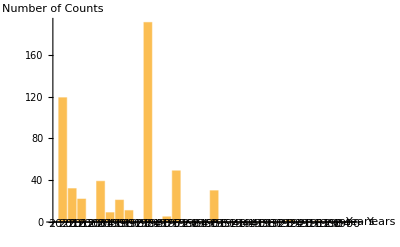

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[democratTexts], republicanNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[democratTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
democratNominee = {"Clinton", "Obama", "Obama", "Kerry", "Gore", "Clinton", "Clinton", "Dukakis", "Mondale", "Carter", "Carter", "McGovern", "Humphrey", "Johnson", "Kennedy", "Stevenson","Stevenson", "Truman", "Roosevelt", "Roosevelt", "Roosevelt", "Roosevelt", "Smith", "Davis", "Cox", "Wilson", "Wilson", "Bryan", "Parker", "Bryan"};
```

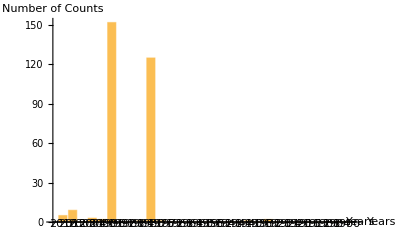

```mathematica
BarChart[MapThread[StringCount[#1, " "~~#2] &, {Values[republicanTexts], democratNominee}], ChartLabels->(StringTake[#, 1;;4]&/@Keys[republicanTexts]), ImageSize->Full, LabelStyle->Tiny, AxesLabel->{"Years", "Number of Counts"}]
```

```mathematica
posnegtrain = ResourceData["Sample Data: Movie Review Sentence Polarity", "TrainingData"]
```

```mathematica
(*Let's think abt this*)
```

```mathematica
sentimentScore[text_,device_:"CPU"]:=With[{output=NetModel["Sentiment Language Model Trained on Amazon Product Review Data"][text,NetPort[{"LastState","Output"}],TargetDevice->device]},Switch[Depth[output],2,output[[2389]],3,output[[All,2389]]]]
```

```mathematica
testingS= TextSentences[Values[democratTexts][[1]]];
```

```mathematica
Round[Length[testingS]/4]
```

381

```mathematica
TextSeValues[democratTexts]
```

```mathematica
RandomSample[#, Round[Length[#]/4]] & /@ Table[TextSentences[p],{p, Values[democratTexts]}]
```

```mathematica
test = sentimentScore /@ RandomSample[#, Round[Length[#]/4]] & /@ Table[TextSentences[p],{p, Values[democratTexts]}];
```

$Aborted

```mathematica
test2 = sentimentScore /@ RandomSample[#, Round[Length[#]/4]] & /@ Table[TextSentences[p],{p, Values[republicanTexts]}];
```

```mathematica
classing = Counts[Table[Which[-0.1 < x < 0.1, "Neutral", x < -0.1, "Negative", x > 0.1, "Positive"], {x, test}]]
```

<|Neutral→261,Positive→101,Negative→19|>

```mathematica
Mean[Table[sentimentScore[s], {s, RandomSample[TextSentences[Values[democratTexts][[1]]], 200]}]]
```

$Aborted

```mathematica
(*up to here*)
```

```mathematica
neutPart = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/political_social_media.csv", "Data", HeaderLines->1]
```

```mathematica
classNeutPart = Table[StringReplace[ToString[s[[21]]], PunctuationCharacter:>""]->s[[8]], {s, neutPart}]
```

```mathematica
indices=RandomSample[Range[Length[libcons]],Min[subsetSize,Length[libcons]]];
```

```mathematica
datasetDown=Values[Keys/@GroupBy[Thread[DimensionReduce[Keys[classlibcons],2,Method->"TSNE"]->Values[classlibcons]],Values]];
```

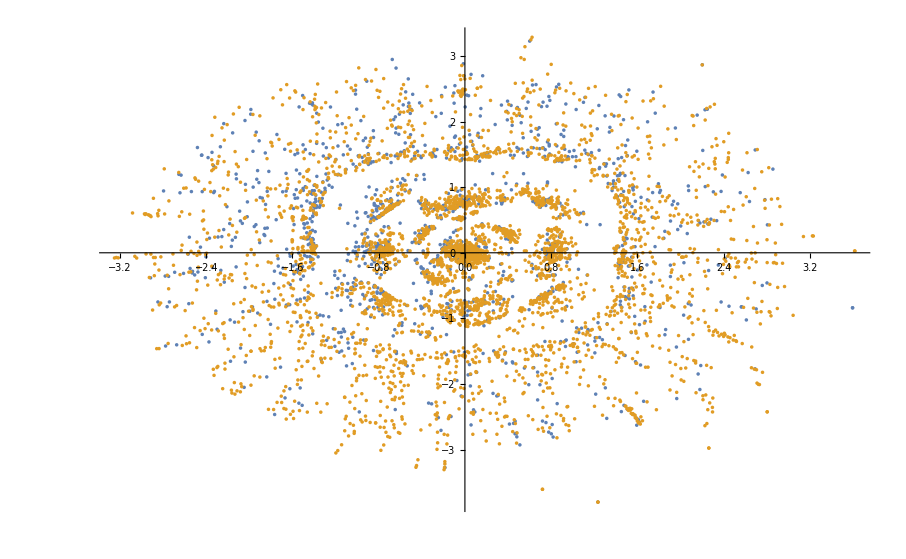

```mathematica
ListPlot[datasetDown]
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][classNeutPart];
```

```mathematica
neutPartF = Classify[trainSet,Method->"RandomForest"]
```

ClassifierFunction[…]

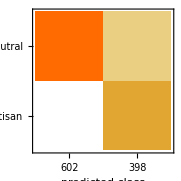
Classifier Measurements
Classifier method | Markov
Number of test examples | 1000
Accuracy | (84.11.2) %
Accuracy baseline | (76.11.3) %
Geometric mean of probabilities | 0.24 ± 0.042
Mean cross entropy | 1.43 ± 0.18
Single evaluation time | 2.42 ms/example
Batch evaluation speed | 3.19 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[neutPartF,testSet]
```

```mathematica
demPartisanCount = Mean[Table[ps["partisan"],{ps, neutPartF[TextSentences[#],"Probabilities"]}]]& /@ Values[democratTexts]
```

{0.703211,0.696444,0.658335,0.654036,0.598425,0.647225,0.664165,0.598313,0.720076,0.698671,0.641517,0.710451,0.722308,0.600104,0.620425,0.671227,0.699819,0.599839,0.62437,0.557367,0.692662,0.616512,0.706971,0.734935,0.703282,0.715068,0.710106,0.786173,0.786319,0.806267,0.79256}

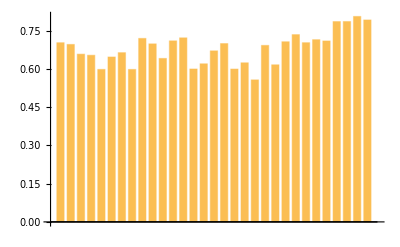

```mathematica
BarChart[demPartisanCount]
```

```mathematica
repPartisanCount = Mean[Table[ps["partisan"],{ps, libconsf[TextSentences[#],"Probabilities"]}]]& /@ Values[republicanTexts]
```

{0.708057,0.684293,0.65792,0.567213,0.663928,0.689252,0.658059,0.631696,0.63709,0.703443,0.669713,0.622125,0.622125,0.696871,0.632323,0.590069,0.717187,0.643967,0.662785,0.74188,0.675587,0.708868,0.68367,0.705545,0.782417,0.813895,0.746157,0.711108,0.741839,0.668466}

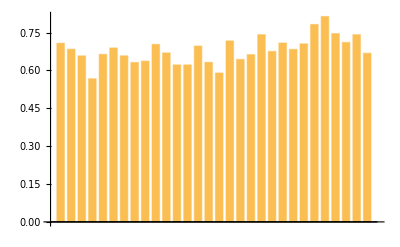

```mathematica
BarChart[repPartisanCount]
```

```mathematica
partisanCount = Counts[libconsf[TextSentences[#]]]&/@ Values[democratTexts]
```

{<|neutral→444,partisan→1081|>,<|partisan→742,neutral→307|>,<|partisan→732,neutral→352|>,<|neutral→366,partisan→744|>,<|partisan→576,neutral→364|>,<|partisan→755,neutral→378|>,<|neutral→270,partisan→563|>,<|partisan→220,neutral→144|>,<|partisan→52,neutral→19|>,<|partisan→1178,neutral→477|>,<|partisan→1056,neutral→574|>,<|neutral→236,partisan→623|>,<|partisan→662,neutral→232|>,<|neutral→257,partisan→402|>,<|partisan→538,neutral→315|>,<|partisan→540,neutral→244|>,<|partisan→384,neutral→155|>,<|neutral→143,partisan→227|>,<|partisan→104,neutral→63|>,<|neutral→35,partisan→46|>,<|neutral→52,partisan→132|>,<|neutral→34,partisan→54|>,<|partisan→31,neutral→14|>,<|partisan→152,neutral→50|>,<|partisan→162,neutral→62|>,<|partisan→139,neutral→50|>,<|partisan→96,neutral→41|>,<|partisan→99,neutral→25|>,<|partisan→84,neutral→22|>,<|partisan→68,neutral→16|>,<|partisan→60,neutral→14|>}

```mathematica
(*Bad*)
```

```mathematica
libCon = Import["/Users/eugenehwang/Work/WSRP2024_Eugene_Hwang/master_df.csv", "Data", HeaderLines->1]
```

```mathematica
removeSet = {"a","about","above","across","after","afterwards","again","against","all","almost","alone","along","already","also","although","always","am","among","amongst","amoungst","amount","amp","an","and","another","any","anyhow","anyone","anything","anyway","anywhere","are","around","as","at","back","be","became","because","become","becomes","becoming","been","before","beforehand","behind","being","below","beside","besides","between","beyond","bill","both","bottom","but","by","call","can","cannot","cant","co","com","con","could","couldnt","cry","de","describe","detail","did","do","does","done","down","due","during","each","eg","eight","either","eleven","else","elsewhere","empty","enough","etc","even","ever","every","everyone","everything","everywhere","except","few","fifteen","fifty","fill","find","fire","first","five","for","former","formerly","forty","found","four","from","front","full","further","get","give","go","had","has","hasnt","have","he","hence","her","here","hereafter","hereby","herein","hereupon","hers","herself","him","himself","his","how","however","https","hundred","i","ie","if","in","inc","indeed","interest","into","is","it","its","itself","just","keep","last","latter","latterly","least","less","like","ltd","made","many","may","me","meanwhile","might","mill","mine","more","moreover","most","mostly","move","much","must","my","myself","name","namely","neither","never","nevertheless","next","nine","no","nobody","none","noone","nor","not","nothing","now","nowhere","of","off","often","on","once","one","only","onto","or","other","others","otherwise","our","ours","ourselves","out","over","own","part","per","perhaps","please","put","rather","re","same","say","says","see","seem","seemed","seeming","seems","serious","several","she","should","show","side","since","sincere","six","sixty","so","some","somehow","someone","something","sometime","sometimes","somewhere","still","such","system","take","ten","than","that","the","their","them","themselves","then","thence","there","thereafter","thereby","therefore","therein","thereupon","these","they","thick","thin","things","third","this","those","though","three","through","throughout","thru","thus","to","together","too","top","toward","towards","twelve","twenty","two","un","under","until","up","upon","us","very","via","want","was","watch","we","well","were","what","whatever","when","whence","whenever","where","whereafter","whereas","whereby","wherein","whereupon","wherever","whether","which","while","whither","who","whoever","whole","whom","whose","why","will","with","within","without","would","www","x200b","yet","you","your","yours","yourself","yourselves"};
```

```mathematica
classLibCon = Table[StringReplace[StringJoin[Riffle[TextWords[ToString[s[[3]]]]/. Table[w->"",{w, removeSet}], " "]], PunctuationCharacter:>""]->If[s[[4]]==0, "Conservative", "Liberal"], {s, libCon}];
```

```mathematica
classLibCon = Table[StringReplace[DeleteStopwords[ToString[s[[3]]]], PunctuationCharacter:>""]->If[s[[4]]==0, "Conservative", "Liberal"], {s, libCon}];
```

```mathematica
{trainSet,testSet}=ResourceFunction["TrainTestSplit"][classLibCon];
```

```mathematica
libConF = Classify[trainSet]
```

ClassifierFunction[…]

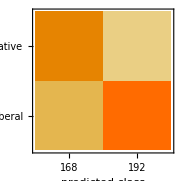
Classifier Measurements
Classifier method | Markov
Number of test examples | 360
Accuracy | (71.12.4) %
Accuracy baseline | (55.62.6) %
Geometric mean of probabilities | 0.336 ± 0.041
Mean cross entropy | 1.09 ± 0.12
Single evaluation time | 2.43 ms/example
Batch evaluation speed | 3.23 examples/ms
-Graphics- |

```mathematica
ClassifierMeasurements[libConF, testSet]
```

```mathematica
libConF = Classify[classLibCon]
```

ClassifierFunction[…]

```mathematica
Counts[libConF[TextSentences[Values[democratTexts][[1]]]]]
```

<|Conservative→1429,Liberal→96|>

```mathematica
testing = Mean[Table[ps["Liberal"],{ps,libConF[TextSentences[#], "Probabilities"]}]] & /@ Values[democratTexts]
```

{0.0906621,0.134686,0.106296,0.108966,0.130673,0.0964915,0.112803,0.0777427,0.0351542,0.0935322,0.0894019,0.0916777,0.0824136,0.076665,0.0430849,0.0780739,0.0827304,0.066213,0.070371,0.0846131,0.0574465,0.0386614,0.00867073,0.0424787,0.0356201,0.0219026,0.052286,0.0139061,0.0154346,0.00471323,0.0222954}

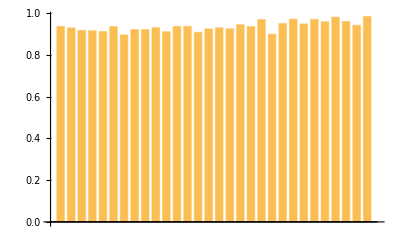

```mathematica
BarChart[testing]
```

```mathematica
(*up to here*)
```

```mathematica
umapDRAll = DimensionReduce[StringReplace[DeleteStopwords[ToLowerCase[#]], PunctuationCharacter :>""]&/@Values[alltexts], FeatureExtractor -> "WordVectors",Method->"UMAP"]
```

{{13.2196,8.99245},{12.5249,9.34378},{13.0667,7.8732},{13.2059,8.19714},{11.4641,9.2855},{12.5171,7.90734},{11.7709,8.75796},{9.47949,10.713},{8.15988,10.8617},{13.4662,11.0433},{11.9908,10.7957},{11.7843,11.2232},{11.1401,10.5001},{10.9663,12.1173},{10.7018,11.9252},{10.0228,11.1598},{9.46137,12.5363},{9.05841,13.1508},{7.45595,12.5513},{4.44376,15.3232},{7.06672,12.7257},{4.71899,13.658},{5.06267,13.5548},{7.86306,15.6723},{7.01178,16.4244},{7.33584,16.3405},{6.04597,14.9152},{6.03453,16.8552},{6.70131,16.7192},{4.96511,16.85},{4.927,16.6891},{14.4459,9.40126},{14.1524,8.68944},{14.4969,9.84121},{14.0548,10.2831},{14.18,8.78852},{14.4787,9.89972},{12.4628,10.0182},{13.7437,10.6144},{13.5208,11.1374},{12.46,11.1122},{11.0546,12.0569},{8.24989,11.3267},{9.46438,11.9171},{8.83462,13.5213},{7.95684,11.6357},{7.47348,11.7009},{7.45057,13.6923},{4.83354,14.884},{6.10262,13.6729},{5.31058,13.3399},{4.42767,14.1471},{7.70564,14.504},{7.1801,14.2625},{7.96984,15.4902},{6.33728,14.5895},{5.21151,15.5025},{4.64757,16.7172},{6.21006,16.933},{4.23163,15.7932},{5.51935,15.3292}}

```mathematica
clusters = FindClusters[umapDRAll, Method->"DBSCAN"];
```

```mathematica
labeledClusters = Table[Table[Callout[c, Keys[alltexts][[Position[umapDRAll, c][[1]][[1]]]]], {c, lst}], {lst, clusters}];
```

```mathematica
ListPlot[labeledClusters, ImageSize->Full]
```

-Graphics-

```mathematica
umapDem = DimensionReduce[Values[democratTexts], FeatureExtractor -> "WordVectors",Method->"UMAP"]
```

{{-2.67434,6.08254},{-2.31095,5.99286},{-3.54602,6.07275},{-4.8112,4.91323},{-3.34861,4.21233},{-4.39267,5.6556},{-4.71054,4.38124},{-2.14425,4.67019},{0.660192,4.70708},{-3.37618,3.56226},{-1.10703,2.64129},{-0.0174895,3.45551},{-2.54372,3.08079},{0.087519,3.77646},{-0.769468,2.95153},{-1.50055,5.19417},{-0.24778,6.07957},{-0.168869,5.85772},{2.27748,5.33726},{4.58389,7.09443},{1.90248,5.10051},{2.81487,5.67868},{4.08627,6.34178},{1.85527,8.52152},{1.56304,7.18014},{3.12836,8.97117},{4.3179,8.45497},{2.00323,8.45381},{3.50569,8.81481},{3.15741,7.60167},{4.61102,7.4387}}

```mathematica
demClusters =FindClusters[umapDem, Method->"DBSCAN"];
```

```mathematica
labeledDemClusters = Table[Table[c->Keys[democratTexts][[Position[umapDem, c][[1]][[1]]]], {c, lst}], {lst, demClusters}];
```

```mathematica
labeledDemClusters
```

{{{-2.14425,4.67019}→1992 Democratic Party,{-1.50055,5.19417}→1960 Democratic Party},{{-2.67434,6.08254}→2020 Democratic Party,{-2.31095,5.99286}→2016 Democratic Party,{-3.54602,6.07275}→2012 Democratic Party,{-4.8112,4.91323}→2008 Democratic Party,{-4.39267,5.6556}→2000 Democratic Party,{-4.71054,4.38124}→1996 Democratic Party},{{1.85527,8.52152}→1928 Democratic Party,{2.00323,8.45381}→1912 Democratic Party},{{3.12836,8.97117}→1920 Democratic Party,{4.3179,8.45497}→1916 Democratic Party,{3.50569,8.81481}→1908 Democratic Party},{{-3.34861,4.21233}→2004 Democratic Party,{-3.37618,3.56226}→1984 Democratic Party,{-2.54372,3.08079}→1972 Democratic Party},{{-1.10703,2.64129}→1980 Democratic Party,{-0.0174895,3.45551}→1976 Democratic Party,{0.087519,3.77646}→1968 Democratic Party,{-0.769468,2.95153}→1964 Democratic Party},{{4.58389,7.09443}→1944 Democratic Party,{4.08627,6.34178}→1932 Democratic Party,{4.61102,7.4387}→1900 Democratic Party},{{3.15741,7.60167}→1904 Democratic Party},{{-0.24778,6.07957}→1956 Democratic Party,{-0.168869,5.85772}→1952 Democratic Party},{{2.27748,5.33726}→1948 Democratic Party,{1.90248,5.10051}→1940 Democratic Party,{2.81487,5.67868}→1936 Democratic Party},{{0.660192,4.70708}→1988 Democratic Party},{{1.56304,7.18014}→1924 Democratic Party}}

```mathematica
ListPlot[labeledDemClusters, ImageSize->Large, PlotLegends->Automatic]
```

-Graphics-

```mathematica
umapRep = DimensionReduce[Values[republicanTexts], FeatureExtractor -> "WordVectors",Method->"UMAP"]
```

{{25.6005,8.16344},{26.456,8.27596},{27.6307,6.78995},{25.7967,6.50091},{27.6511,5.84632},{27.5523,5.86485},{27.1627,7.71421},{26.1919,4.43929},{26.6833,4.76299},{27.6899,6.84113},{24.7256,6.58145},{23.5703,7.2307},{22.6305,5.79721},{23.3335,6.36765},{22.2662,7.85435},{21.5667,5.88485},{21.3422,8.31927},{18.5446,10.3426},{20.8445,7.94347},{19.6629,10.0966},{20.691,9.26773},{18.6053,6.58704},{19.9146,6.40499},{19.6849,8.02377},{20.5306,6.6678},{16.783,8.84603},{18.0186,7.71346},{18.2047,7.47153},{16.9133,9.08465},{18.0821,9.38669}}

```mathematica
repClusters =FindClusters[umapRep, Method->"DBSCAN"];
```

```mathematica
labeledRepClusters = Table[Table[c->Keys[republicanTexts][[Position[umapRep, c][[1]][[1]]]], {c, lst}], {lst, repClusters}]
```

{{{16.783,8.84603}→1916 Republican Party,{16.9133,9.08465}→1904 Republican Party,{18.0821,9.38669}→1900 Republican Party},{{22.2662,7.85435}→1960 Republican Party,{21.3422,8.31927}→1952 Republican Party,{20.8445,7.94347}→1944 Republican Party,{19.6849,8.02377}→1924 Republican Party},{{18.5446,10.3426}→1948 Republican Party,{19.6629,10.0966}→1940 Republican Party},{{25.7967,6.50091}→2004 Republican Party,{24.7256,6.58145}→1976 Republican Party,{22.6305,5.79721}→1968 Republican Party,{23.3335,6.36765}→1964 Republican Party,{21.5667,5.88485}→1956 Republican Party},{{27.6511,5.84632}→2000 Republican Party,{27.5523,5.86485}→1996 Republican Party},{{27.6307,6.78995}→2008 Republican Party,{27.6899,6.84113}→1980 Republican Party},{{23.5703,7.2307}→1972 Republican Party},{{18.0186,7.71346}→1912 Republican Party,{18.2047,7.47153}→1908 Republican Party},{{18.6053,6.58704}→1932 Republican Party,{19.9146,6.40499}→1928 Republican Party,{20.5306,6.6678}→1920 Republican Party},{{26.1919,4.43929}→1988 Republican Party,{26.6833,4.76299}→1984 Republican Party},{{20.691,9.26773}→1936 Republican Party},{{25.6005,8.16344}→2016 Republican Party,{26.456,8.27596}→2012 Republican Party,{27.1627,7.71421}→1992 Republican Party}}

```mathematica
ListPlot[labeledRepClusters, ImageSize->Large, PlotLegends->Automatic]
```

-Graphics-

```mathematica
textWordsDem = Join[WordStem /@TextWords[StringJoin[Table[StringDelete[StringReplace[DeleteStopwords[ToLowerCase[democratTexts[y]]], PunctuationCharacter :>""], DigitCharacter..], {y, Values[#]}]]]]& /@ labeledDemClusters;
```

```mathematica
demWordTF =Reverse[SortBy[Table[{w[[1]], w[[2]]/Length[#]}, {w,N[Tally[#]]}], Last]] & /@ textWordsDem
```

```mathematica
demWordIDF = Table[{w[[1]],Log[N[Length[textWordsDem]/Length[Select[textWordsDem, MemberQ[#, w[[1]]] &]]]]}, {w, #}] &/@demWordTF
```

```mathematica
tfidfDem = Select[Reverse[SortBy[Table[{demWordTF[[#]][[i]][[1]], demWordTF[[#]][[i]][[2]] * demWordIDF[[#]][[i]][[2]]}, {i, Range[Length[demWordTF[[#]]]]}], Last]], ResourceFunction["NounQ"][#[[1]]] &,10][[All,1]] & /@ Range[Length[demWordTF]]
```

{{program,bush,help,job,health,communist,access,atom,drug,research},{trump,gore,student,health,job,help,access,internet,drug,clean},{telegraph,raiser,battleship,c,toil,rascal,favor,express,tariff,b},{pulp,speaker,favor,panic,medium,workingman,exhibit,port,prison,render},{job,bush,drug,health,environment,soviet,program,help,john,cut},{program,soviet,percent,carter,health,job,goal,implement,help,student},{silver,liquor,plea,plank,paper,uplift,temper,saloon,imperialist,freemen},{passport,frame,sailor,woe,weal,truce,trammel,spectacular,sharer,proverb},{program,atom,stunt,help,soviet,communist,health,brotherhood,bluster,goal},{program,youth,implement,health,leadership,chart,million,wheat,radio,launch},{environment,drug,help,revers,homeless,coast,health,weapon,soviet,partnership},{shoal,barter,taint,referendum,cordial,leas,toiler,slaughter,p,flat}}

```mathematica
textWordsRep= Join[WordStem /@TextWords[StringJoin[Table[StringDelete[StringReplace[DeleteStopwords[ToLowerCase[republicanTexts[y]]], PunctuationCharacter :>""], DigitCharacter..], {y, Values[#]}]]]]& /@ labeledRepClusters;
```

```mathematica
repWordTF =Reverse[SortBy[Table[{w[[1]], w[[2]]/Length[#]}, {w,N[Tally[#]]}], Last]] & /@ textWordsRep
```

```mathematica
repWordIDF = Table[{w[[1]],Log[N[Length[textWordsRep]/Length[Select[textWordsRep, MemberQ[#, w[[1]]] &]]]]}, {w, #}] &/@repWordTF
```

```mathematica
tfidfRep = Select[Reverse[SortBy[Table[{repWordTF[[#]][[i]][[1]], repWordTF[[#]][[i]][[2]] * repWordIDF[[#]][[i]][[2]]}, {i, Range[Length[repWordTF[[#]]]]}], Last]], ResourceFunction["NounQ"][#[[1]]] &,10][[All,1]] & /@ Range[Length[repWordTF]]
```

{{cordial,statesman,tender,countrymen,gold,statesmanship,sailor,neutral,earnest,upright},{program,annum,communist,atom,help,research,leadership,progress,growth,assist},{teamwork,mob,brotherhood,whirl,treason,rearmament,incident,hoof,descent,column},{bush,terrorist,help,terror,program,access,percent,leadership,job,goal},{dole,bob,access,bush,environment,bill,governor,agenda,role,percent},{carter,soviet,access,percent,program,job,neighborhood,role,growth,goal},{program,help,leadership,addition,job,young,passport,poor,soviet,train},{session,firemen,derelict,telegraph,seamen,panic,statesmanship,militia,domain,writ},{eighteenth,discount,coven,comfort,congressmen,leadership,bank,debtor,earnest,railroad},{soviet,percent,program,parent,job,ranch,help,s,drug,growth},{dishonor,autocrat,sweatshop,purport,protector,fright,wild,tender,swarm,coin},{bush,access,job,abort,like,current,internet,environment,parent,student}}